```mathematica
H = H0 * Sqrt[Ωm*(1+z)^3+Ωϕ];
e1=(1+z)^2*H^2*G''[z] + ((1+z)^2*H*D[H,z]-(1+z)*H^2)*G'[z]-3/2*Ωm*H0^2*(1+z)^3*G[z]==0;
sol=NDSolve[{e1/.{H0->100*0.710,Ωm->0.222+0.045,Ωϕ->0.733},G[9]==1,G'[9]==-0.1},G[z],{z,0,9}]
```

{{G[z]→InterpolatingFunction[{{0., 9.}}, <>][z]}}

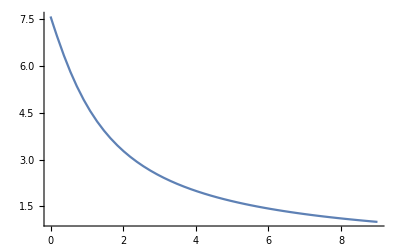

```mathematica
Plot[G[z]/.sol,{z,0,9},PlotRange->All]
```

```mathematica
Hz=H0*Sqrt[e];
e=Ωm(1+z)^3+Ωr(1+z)^4+Ωk(1+z)^2+Ωϕ*E^(3*Integrate[(1+w0+wa*zp/(1+zp))/(1+zp),{zp,0,z},Assumptions->{z>=0,z∈Reals}]);
```

```mathematica
D[Hz,z]*Hz//Simplify
```

1/2 H0^2 (1+z) (2 Ωk+3 (1+z) Ωm+4 (1+z)^2 Ωr+3 ⅇ^(-(3 wa z)/(1+z)) (1+z)^(3 (w0+wa)) (1+w0+z+w0 z+wa z) Ωϕ)

```mathematica
H = H0 * Sqrt[Ωm*(1+z)^3+Ωr*(1+z)^4+Ωk*(1+z)^2+Ωϕ(1+z)^(3+3w0+3wa)E^(-3wa/(1+z))];
e1=(1+z)^2*H^2*G''[z] + ((1+z)^2*H*D[H,z]-(1+z)*H^2)*G'[z]-3/2*Ωm*H0^2*(1+z)^3*G[z]==0;
sol=NDSolve[{e1/.{H0->100*0.710,Ωm->0.222+0.045,Ωϕ->0.733,w0->-1,wa->0,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G[z],{z,0,9}]
```

{{G[z]→InterpolatingFunction[{{0., 9.}}, <>][z]}}

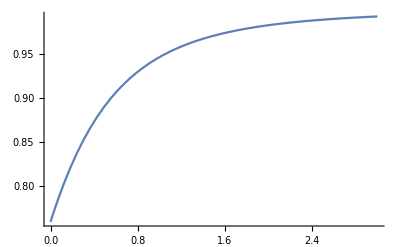

```mathematica
Plot[(1+z)*G[z]/10/.sol,{z,0,3},PlotRange->All]
```

```mathematica
e2=w0^2*H0^2*G''[z] + (w0^2*H0^2/2-w0*H0^2)*G'[z]-3/2*Ωm*H0^2*w0^3*G[z]==0;
sol=NDSolve[{e2/.{H0->100*0.710,Ωm->0.222+0.045,Ωϕ->0.733,w0->-1,wa->0,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G[z],{z,0,9}]
```

{{G[z]→InterpolatingFunction[{{0., 9.}}, <>][z]}}

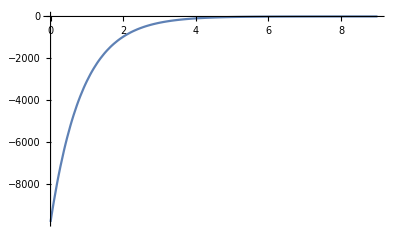

```mathematica
Plot[G[z]/.%8,{z,0,9},PlotRange->All]
```